### Start choosing the example:

```mathematica
t=14;
beta = 0;
A = 0.2;
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15,S1->0, S2->0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.155377 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.194062,Null}

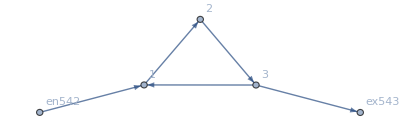

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j544→80/3,j545→80/3,j546→0,j547→80,j548→80,j549→0,j550→0,j551→160/3,j552→0,j553→0,jt554→0,jt555→0,jt556→0,jt557→0,jt558→80/3,jt559→160/3,jt560→80/3,jt561→0,jt562→0,jt563→80/3,jt564→0,jt565→160/3,jt566→0,jt567→0,u568→205/3,u569→125/3,u570→15,u571→15,u572→205/3,u573→125/3,u574→15,u575→205/3,u576→15,u577→205/3|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0179586

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0177279

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0174905

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0172467

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0169969

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0167415

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0164808

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0162152

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.015945

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0156705

<|j544→20.5557,j545→20.5557,j546→0,j547→80,j548→80,j549→0,j550→0,j551→59.4443,j552→0,j553→0,jt554→0,jt555→0,jt556→0,jt557→0,jt558→20.5557,jt559→59.4443,jt560→20.5557,jt561→0,jt562→0,jt563→20.5557,jt564→0,jt565→59.4443,jt566→0,jt567→0,u568→18.0523,u569→16.5261,u570→15.,u571→15,u572→18.0523,u573→16.5261,u574→15.,u575→18.0523,u576→15,u577→18.0523|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0201858

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0198039

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0194149

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0190197

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.018619

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0182136

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0178043

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0173918

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0169767

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0165597

<|j544→20.0153,j545→20.0153,j546→0,j547→80,j548→80,j549→0,j550→0,j551→59.9847,j552→0,j553→0,jt554→0,jt555→0,jt556→0,jt557→0,jt558→20.0153,jt559→59.9847,jt560→20.0153,jt561→0,jt562→0,jt563→20.0153,jt564→0,jt565→59.9847,jt566→0,jt567→0,u568→18.6027,u569→16.8013,u570→15.,u571→15,u572→18.6027,u573→16.8013,u574→15.,u575→18.6027,u576→15,u577→18.6027|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0259476

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0249064

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0238756

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0228586

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0218582

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0208768

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0199166

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0189794

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0180665

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0171791

<|j544→18.9805,j545→18.9805,j546→0,j547→80,j548→80,j549→0,j550→0,j551→61.0195,j552→0,j553→0,jt554→0,jt555→0,jt556→0,jt557→0,jt558→18.9805,jt559→61.0195,jt560→18.9805,jt561→0,jt562→0,jt563→18.9805,jt564→0,jt565→61.0195,jt566→0,jt567→0,u568→20.261,u569→17.6305,u570→15.,u571→15,u572→20.261,u573→17.6305,u574→15.,u575→20.261,u576→15,u577→20.261|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0369234

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0166028

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00746454

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.003356

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00150885

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000678377

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000304999

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000137128

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000616529

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000277193

<|j544→24.5232,j545→24.5232,j546→0,j547→80,j548→80,j549→0,j550→0,j551→55.4768,j552→0,j553→0,jt554→0,jt555→0,jt556→0,jt557→0,jt558→24.5232,jt559→55.4768,jt560→24.5232,jt561→0,jt562→0,jt563→24.5232,jt564→0,jt565→55.4768,jt566→0,jt567→0,u568→48.009,u569→31.5045,u570→15.,u571→15,u572→48.009,u573→31.5045,u574→15.,u575→48.009,u576→15,u577→48.009|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[6.96187×10^-14,ComplexInfinity]

<|j544→80/3,j545→80/3,j546→0,j547→80,j548→80,j549→0,j550→0,j551→160/3,j552→0,j553→0,jt554→0,jt555→0,jt556→0,jt557→0,jt558→80/3,jt559→160/3,jt560→80/3,jt561→0,jt562→0,jt563→80/3,jt564→0,jt565→160/3,jt566→0,jt567→0,u568→205/3,u569→125/3,u570→15,u571→15,u572→205/3,u573→125/3,u574→15,u575→205/3,u576→15,u577→205/3|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.617897

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.929008

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.13378

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.0854

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.02683

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00474

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00036

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00001

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

<|j1279→0,j1280→0.,j1281→0,j1282→80.,j1283→80.,j1284→2.84967×10^23,j1285→2.84967×10^23,j1286→2.84967×10^23,j1287→0.,j1288→0.,jt1289→2.84967×10^23,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→0.,jt1294→80.,jt1295→0.,jt1296→2.84967×10^23,jt1297→0.,jt1298→0.,jt1299→2.84967×10^23,jt1300→80.,jt1301→0.,jt1302→0.,u1303→4.02653×10^8,u1304→2.01327×10^8,u1305→15.,u1306→15.,u1307→4.36208×10^8,u1308→2.01327×10^8,u1309→15.,u1310→4.36208×10^8,u1311→15.,u1312→4.36208×10^8|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00001

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«6 more identical outputs»

<|j1279→0,j1280→0.,j1281→0,j1282→80.,j1283→80.,j1284→1.25521×10^189,j1285→1.25521×10^189,j1286→1.25521×10^189,j1287→0.,j1288→0.,jt1289→1.25521×10^189,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→0.,jt1294→80.,jt1295→0.,jt1296→1.25521×10^189,jt1297→0.,jt1298→0.,jt1299→1.25521×10^189,jt1300→80.,jt1301→0.,jt1302→0.,u1303→0.,u1304→0.,u1305→15.,u1306→15.,u1307→0.,u1308→0.,u1309→15.,u1310→0.,u1311→15.,u1312→0.|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«1 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[2.91800775518775×10^390-1. j544+1. j549-IntM[-80+j544-j549]]^2+2 Abs[2.91800775518775×10^390-1. j544+1. j549-IntM[j544-j549]]^2),(√(Abs[2.91800775518775×10^390-1. j544+1. j549-IntM[-80+j544-j549]]^2+2 Abs[2.91800775518775×10^390-1. j544+1. j549-IntM[j544-j549]]^2))/(√3 Abs[2.91800775518775×10^390+0. j544+0. j549]),(√(Abs[2.91800775518775×10^390-1. j544+1. j549-IntM[-80+j544-j549]]^2+2 Abs[2.91800775518775×10^390-1. j544+1. j549-IntM[j544-j549]]^2))/(√(Abs[-80+j544-j549+IntM[-80+j544-j549]]^2+2 Abs[j544-j549+IntM[j544-j549]]^2))]

ReplaceAll::reps: {u569==u573&&u570==15&&u572==u575&&u574==15&&j544-j549-u568+u573==j544-j549+IntM[j544-j549]&&j544-j549-u569+u574==j544-j549+IntM[j544-j549]&&-80+j544-j549-u570+u575==-80+j544-j549+IntM[-80+j544-j549]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AssociateTo::invlb: The argument u569==u573&&u570==15&&u572==u575&&u574==15&&j544-j549-u568+u573==j544-j549+IntM[j544-j549]&&j544-j549-u569+u574==j544-j549+IntM[j544-j549]&&-80+j544-j549-u570+u575==-80+j544-j549+IntM[-80+j544-j549] is not a list, Rule, or Association.

ReplaceAll::reps: {u569==u573&&u570==15&&u572==u575&&u574==15&&j544-j549-u568+u573==j544-j549+IntM[j544-j549]&&j544-j549-u569+u574==j544-j549+IntM[j544-j549]&&-80+j544-j549-u570+u575==-80+j544-j549+IntM[-80+j544-j549]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«7 more identical outputs»

<|j1279→0,j1280→0.,j1281→0,j1282→80.,j1283→80.,j1284→1.23536349271862×10^859,j1285→1.23536349271862×10^859,j1286→1.23536349271862×10^859,j1287→0.,j1288→0.,jt1289→1.23536349271862×10^859,jt1290→0.,jt1291→0.,jt1292→0.,jt1293→0.,jt1294→80.,jt1295→0.,jt1296→1.23536349271862×10^859,jt1297→0.,jt1298→0.,jt1299→1.23536349271862×10^859,jt1300→80.,jt1301→0.,jt1302→0.,u1303→0``-843.7392649841213,u1304→0``-843.4382349884572,u1305→15.,u1306→15.,u1307→0``-843.4382349884572,u1308→0``-843.4382349884572,u1309→15.,u1310→0``-843.4382349884572,u1311→15.,u1312→0.|>

$Aborted

$Aborted

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«4 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«4 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«1 more identical outputs»

<|j544→0,j545→0,j546→0,j547→80,j548→80,j549→2.62614×10^47,j550→2.62614×10^47,j551→2.62614×10^47,j552→0,j553→0,jt554→2.62614×10^47,jt555→0,jt556→0,jt557→0,jt558→0,jt559→80,jt560→0,jt561→2.62614×10^47,jt562→0,jt563→0,jt564→2.62614×10^47,jt565→80,jt566→0,jt567→0,u568→0.,u569→0.,u570→15.,u571→15,u572→0.,u573→0.,u574→15.,u575→0.,u576→15,u577→0.|>